## Config

```mathematica
(* Provide the location of the randgeom executable *)
(* On windows change randgeom to randgeom.exe *)
programlocation = "/home/mgv29/Desktop/randgeom"
```

/home/mgv29/Desktop/randgeom

```mathematica
(* Test the program. If it return False, check the programlocation provided. If it still does not work, first test randgeom from the console. *)
FileExistsQ[programlocation]&&ListQ[RunThrough["'"<>programlocation<>"'",""]]
```

True

## Useful functions

```mathematica
(* the following just runs randgeom with the specified parameters and parses the output as Mathematica code *)
generateMaps[type_,size_,number_]:=RunThrough["'"<>programlocation<>"' -t"<>type<>" -s"<>ToString[size]<>" -n"<>ToString[number], ""];
generateMap[type_,size_]:=First@generateMaps[type,size,1];
```

```mathematica
(* given a permutation p of {1,2,...,n}, cycles[p] gives the partition of {1,2,...,n} into cycles *)
cycles[p_]:=PermutationCycles[p,Identity];
(* given a list plist of permutations, orbits[plist] gives the partition of {1,2,...,n} into orbits under the permutations *)
orbits[plist_]:=GroupOrbits@PermutationGroup[PermutationCycles/@plist]
```

```mathematica
(* edges, vertices and faces correspond to cycles of halfedge-permutations *)
edgecycles[map_]:=cycles[map[[All,3]]];
facecycles[map_]:=cycles[map[[All,1]]];
vertexcycles[map_]:=cycles[map[[map[[All,3]],1]]];
(* We may assign id's to the vertices of map according to their position in vertexcycles[map] *)
halfedgeToVertexId[map_]:=Dispatch[Join@@MapIndexed[#1->#2[[1]]&,vertexcycles[map],{2}]];
halfedgeToFaceId[map_]:=Dispatch[Join@@MapIndexed[#1->#2[[1]]&,facecycles[map],{2}]];
```

```mathematica
(* functions to construct a Mathematica Graph object *)
uniqueEdges[map_]:=Union[Sort/@(edgecycles[map]/.halfedgeToVertexId[map])];
uniqueDualEdges[map_]:=Union[Sort/@(edgecycles[map]/.halfedgeToFaceId[map])];
mapGraph[map_]:=With[{edges=uniqueEdges[map]},Graph[Union@@edges,#[[1]]<->#[[2]]&/@edges,GraphLayout->None]];
mapDualGraph[map_]:=With[{edges=uniqueDualEdges[map]},Graph[Union@@edges,#[[1]]<->#[[2]]&/@edges,GraphLayout->None]];
```

```mathematica
adj
```

adj

```mathematica
edgecycles[adj]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

PermutationCycles::perm: Symbol[] is not a valid permutation.

PermutationCycles[Symbol[],Identity]

```mathematica
generateMap["C", 3]
```

{{3,6,2},{12,9,1},{4,1,4},{6,3,3},{7,10,6},{1,4,5},{8,5,8},{10,7,7},{2,11,10},{5,8,9},{9,12,12},{11,2,11}}

## Plotting

```mathematica
(* the following is a bit of a hack to extract coordinates from GraphPlot3D's embedding of a graph *)
get3DGraphEmbedding[edg_,method_]:=(VertexCoordinateRules /. Cases[GraphPlot3D[#[[1]]->#[[2]]&/@edg,Method->method], _Rule, Infinity])[[Ordering@DeleteDuplicates[Join@@(List@@@edg)]]];
```

```mathematica
(* one can play with the options here to adapt the embedding *)
coordinates[map_]:=get3DGraphEmbedding[uniqueEdges[map],{"SpringElectricalEmbedding","InferentialDistance"->Automatic,"RepulsiveForcePower"->-2.4}];
```

```mathematica
(* assign colors to faces according to closeness centrality *)
colorFunction[x_]:=ColorData["Rainbow"][Round[Max[Min[0.55-0.15x,1],0],1/40]];
centralityColors[map_]:=colorFunction/@Standardize@ClosenessCentrality[mapDualGraph[map]];
```

```mathematica
plotMap3D[map_,coor_]:=Graphics3D[{EdgeForm[None],{FaceForm[#[[1]]],Polygon[coor[[#[[2,;;3]]]]],If[Length[#[[2]]]==4,Polygon[coor[[#[[2,{1,3,4}]]]]],{}]}&/@Transpose[{centralityColors[map],facecycles[map]/.halfedgeToVertexId[map]}]},Boxed->False]
```

```mathematica
map=generateMap["C",500];
plotMap3D[map,coordinates[map]]
```

Part::partd: Part specification VertexCoordinateRules⟦{1,2,3,19,20,25,26,31,32,35,«492»}⟧ is longer than depth of object.

Part::pkspec1: The expression VertexCoordinateRules cannot be used as a part specification.

Part::partw: Part {1,1,3} of VertexCoordinateRules⟦{1,2,3,19,20,25,26,31,32,35,«492»}⟧ does not exist.

Part::partw: Part {2,1,495} of VertexCoordinateRules⟦{1,2,3,19,20,25,26,31,32,35,«492»}⟧ does not exist.

Part::partw: Part {2,495,496} of VertexCoordinateRules⟦{1,2,3,19,20,25,26,31,32,35,«492»}⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

```mathematica
(* Task: plot geometries of various sizes and models. What are the qualitative differences between the models? *)
```

```mathematica
(* Task: produce some nice pictures. To save a nice picture, one may use something like Export["picture.png",ImageCrop@Rasterize[plot,ImageSize->800,Background->None]] *)
```

## Geodesic two-point function

```mathematica
(* Mathematica has built in support for graph distances: this returns a list of distances from all vertices to a randomly chosen vertex *)
distanceListFromRandomPoint[graph_]:=GraphDistance[graph,RandomChoice@VertexList[graph]];
```

```mathematica
(* produce a histogram with the fraction of points at distance 0,1,2,3,... *)
distanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapGraph[map];
dualDistanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapDualGraph[map];
```

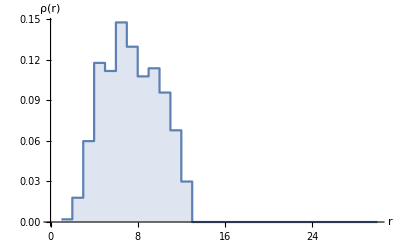

```mathematica
(* An example of a distance profile (from a random vertex) for a single random geometry *)
ListPlot[distanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

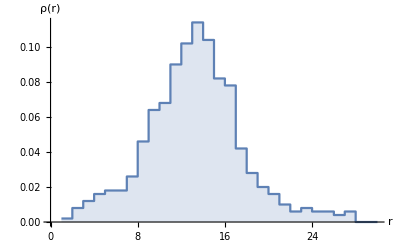

```mathematica
(* the same but for dual graph distance *)
ListPlot[dualDistanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

```mathematica
(* Task: Proceed to gather data for the average distance profile for different system sizes and models, and attempt finite-size scaling to extract the Hausdorff dimension *)
```

## Spectral dimension

The spectral dimension d_s of a map is related to the probability p(t) that a simple random walk on the map (or its dual) returns to its starting point after t steps: p(t) ~ t^(-d_s/2) for 1<< t << n (where n is the system size). There are various ways to measure this return probability: one can simulate a random walker and just record its returns; study a heat diffusion process; or use linear algebra as follows. The return probability ⟨p(t)⟩ averaged over all starting points of the map is related to the normalized adjacency matrix A via  ⟨p(t)⟩=Tr(A^t)/n = ∑λ_i^t/n, where λ_i are the eigenvalues of A.

```mathematica
dualAdjacencyMatrix[map_]:=Module[{dualedges,matrixentries,facedegrees},
dualedges=edgecycles[map]/.halfedgeToFaceId[map];
facedegrees=Length/@facecycles[map];
matrixentries =Tally@Join[dualedges,Reverse/@dualedges];
SparseArray[#[[1]]->#[[2]]/facedegrees[[#[[1,1]]]]&/@matrixentries]
]
```

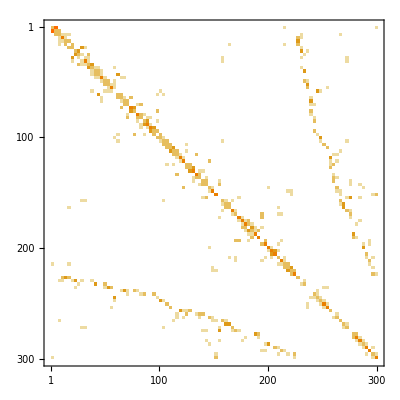

```mathematica
(* plot the adjacency matrix (for fun) *) 
MatrixPlot[dualAdjacencyMatrix[generateMap["D",300]]]
```

```mathematica
dualAdjacencySpectrum[map_]:=Sort@Eigenvalues@Normal@N@dualAdjacencyMatrix[map]
```

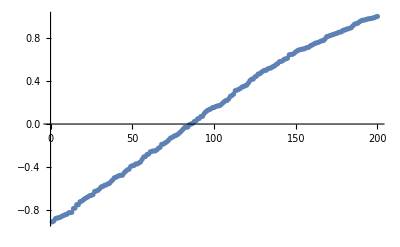

```mathematica
(* a plot of the spectrum of a random geometry *)
ListPlot[dualAdjacencySpectrum[generateMap["A",200]]]
```

```mathematica
(* The return probability of a random walker after k steps averaged over all starting points. *)
(* Notice one can may take range to be e.g. 2^Range[14] to get the return probability for {t=2,t=4,...,t=2^14} without problem. *)
returnProbability[map_,range_]:=With[{spec=dualAdjacencySpectrum[map]},Table[{t,Mean[spec^t]},{t,range}]]
```

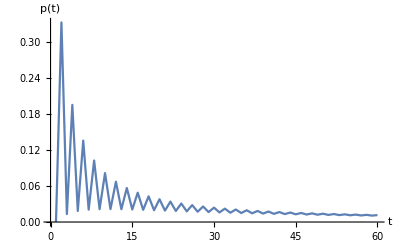

```mathematica
(* A plot of the return probability for a single random geometry *)
(* Notice the alternating pattern. Do you understand why it occurs? *)
ListPlot[returnProbability[generateMap["D",500],Range[60]],Joined->True,AxesLabel->{"t","p(t)"},PlotRange->All]
```

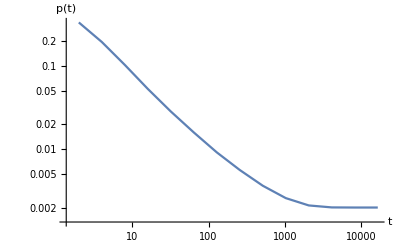

```mathematica
(* A logarithmic plot of the return probability for a single random geometry at large time, showing the finite size effects *)
(* The return probability approaches a constant at late times. What value does it take? *)
ListLogLogPlot[returnProbability[generateMap["A",500],2^Range[14]],Joined->True,AxesLabel->{"t","p(t)"}]
```

```mathematica
(* Task: Gather data for various system sizes and models and try to extract the spectral dimension by fitting the slope (in the logarithmic plot) *)
```

## Susceptibility exponent / counting exponent

Another important exponent is the susceptibility exponent γ (also known as the counting exponent) which governs the growth of the (unlabeled) partition function with increasing system size:  Z(n)~n^(γ-3)ⅇ^(-c n) (assuming we have no marking/root). One way to determine this exponent is to look for minimal necks in the map, i.e. closed paths of minimal length on the map (which for our purposes is typically length 2). For each minimal neck one may determine the distribution of the number m of faces/edges/vertices it encloses. This distribution should for large n,m be proportional to (m(n-m))^(γ-2), and fitting the data provides an estimate for γ. Be aware that for this measurement to work one needs an abundance of minimal necks, which is not necessarily the case for all models.

```mathematica
(* Below is a crude way to identify minimal necks. Do you know of a better way? *)
```

```mathematica
(* find pairs of vertices with more than one connecting edge *)
vertexPairsWithDoubleEdges[map_]:=Select[Normal@GroupBy[edgecycles[map]//Transpose[{#,#/.halfedgeToVertexId[map]}]&,Sort@Last@#&],Length[#[[2]]]>1&][[All,1]];
```

```mathematica
(* a brute force way to determine the (smallest of the two) enclosed volumes: remove the pair of vertices from the graph, and determine the sizes of the remaining connected components *)
componentSize[graph_,vertexpair_]:=Min[#,VertexCount[graph]-#]&@Length@RandomChoice@WeaklyConnectedComponents@VertexDelete[graph,vertexpair]
```

```mathematica
(* an example of the number of vertices in all the regions enclosed by minimal necks in a single random geometry *)
map=generateMap["C",200];
graph=mapGraph[map];
componentSize[mapGraph[map],#]&/@vertexPairsWithDoubleEdges[map]
```

{1,1,1,1,1,1,13,1,1,1,1,1,1,1,10,1,9,5,3,2,1,2,1,2,2,3,5,6,1,1,11,2,3,2,1,1,6,2,1,1,1,4,1,3,1,1,1,1,1,11,4,3,8,3,1,1,1,1,1,1,4,3,5,2,1,4,6,3,1,1,3,6,1,1,1,1,2,1,1,2,1,1}

```mathematica
(* Task: Produce histograms for the volume enclosed by minimal necks in random geometries of various sizes and models; make a logarithmic plot of the histogram (normalized by 1/V where V is the number of vertices of the geometry) against n(1-n/V) and extract γ from the slope of the curve. *)
```

## Python execution

```mathematica
session = StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[session, "import sys; sys.path.append(\"../2d_QG\")"]
```

```mathematica
ExternalEvaluate[session, File["../2d_QG/main.py"]]
(map = ExternalEvaluate[session, "map"] )//Short
```

{{2,3,270},{3,1,269},{1,2,30},{5,6,267},{6,4,141},{4,5,268},{8,9,145},{9,7,226},{7,8,146},{11,12,98},{12,10,12},{10,11,11},«277»,{291,289,205},{289,290,241},{293,294,293},{294,292,292},{292,293,53},{296,297,81},{297,295,61},{295,296,70},{299,300,84},{300,298,190},{298,299,113}}

## Config

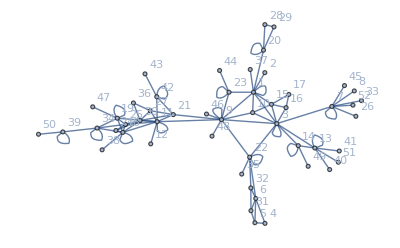

```mathematica
G = mapGraph[map]
GraphPlot[G, VertexLabels->Automatic]
```

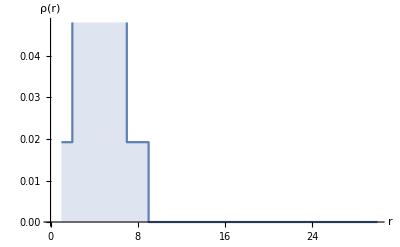

```mathematica
ListPlot[distanceProfile[map,30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```